```mathematica
(* Define default values for parameteres here *)

γ20=1;
(* 
	Vacuum Ω = 0 γ20;
	PBG    Ω = 2 γ20;
	PBG    Ω = 5 γ20; 
*)
Ω=5 γ20;

ϕc=-π/2;
γ10=0.5 γ20;
ω21= γ20;
θ=0;
η=1;
ϕp=0;
tmin=0;
tmax=20;
step=0.001;
```

```mathematica
(* Numerical Solution of the problem and density matrix evaluation part *)
eqs={
c1'[t]==-γ10 c1[t]+(Ω Exp[I ϕc]-η Sqrt[γ10 γ20]Exp[-I ω21 t])c2[t],
c2'[t]==-γ20 c2[t]-(Ω Exp[-I ϕc]+η Sqrt[γ10 γ20]Exp[I ω21 t])c1[t],
c2[0]==Cos[θ],
c1[0]==Sin[θ]Exp[I ϕp]
};

vars={c1,c2};
sol=NDSolve[eqs,vars,{t,tmin,tmax},StartingStepSize->step,Method->{"FixedStep",Method->"ExplicitEuler"}];

data=Table[Flatten@{t,c1[t]/.sol,c2[t]/.sol},{t,tmin,tmax,step}];
(*Export["data.txt",data,"TSV"];*)

For[i=1,i≤Length[data],i++,
ρv11=data[[i,2]]*Conjugate[data[[i,2]]];
ρv12=data[[i,2]]*Conjugate[data[[i,3]]];
ρv21=data[[i,3]]*Conjugate[data[[i,2]]];
ρv22=data[[i,3]]*Conjugate[data[[i,3]]];
ρv33=1-ρv11-ρv22;
ttv[i]=data[[i,1]];
ρ[i]={ttv[i],{{ρv11,ρv12,0},{ρv21,ρv22,0},{0,0,ρv33}}};
];
ρ11=Table[ρ[i][[2,1,1]],{i,1,Length[data]}];
ρ12=Table[ρ[i][[2,1,2]],{i,1,Length[data]}];
ρ21=Table[ρ[i][[2,2,1]],{i,1,Length[data]}];
ρ22=Table[ρ[i][[2,2,2]],{i,1,Length[data]}];
ρ33=Table[ρ[i][[2,3,3]],{i,1,Length[data]}];
tt=Table[ttv[i],{i,1,Length[data]}];
```

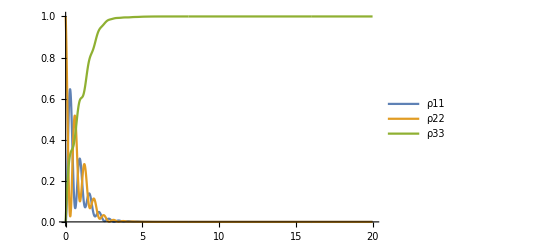

```mathematica
ListLinePlot[{Transpose@{tt,Re[ρ11]},Transpose@{tt,Re[ρ22]},Transpose@{tt,Re[ρ33]}},PlotRange->All,PlotLegends->{"ρ11","ρ22","ρ33"}]
```

```mathematica
entropy=Array[0,0];
eigval=Array[0,0];
eigvec=Array[0,0];
For[i=1,i≤Length[data],i++,
tmp=ρ[i][[2]];
AppendTo[eigval,Eigenvalues[tmp]];
AppendTo[eigvec,Eigenvectors[tmp]];
AppendTo[entropy,-N[Total[Eigenvalues[tmp]*Log[Eigenvalues[tmp]]]]];
];
ListLinePlot[Transpose@{tt,entropy},PlotRange->All]
```

```mathematica
eigval[[1]]
eigvec[[1]]
```

{1.,0.,0.}

{{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}